```mathematica
(*Voici la récurrence qui calcule la somme des contributions de feynman, motif triangulaire, porte de Hadamard (le suel cgt de signe se produit quand le photon traverse la lame de S en N*)
```

```mathematica
c[0]=f[0,0];c[i_]:=c[i-1]/.f[x_,c_]->(f[x-1,0]+(-1)^c f[x+1,1])/(√2)//Simplify
```

```mathematica
c[1]
```

(f[-1,0]+f[1,1])/(√2)

```mathematica
c[2]
```

1/2 (f[-2,0]+f[0,0]+f[0,1]-f[2,1])

```mathematica
c[32]
```

1/65536(f[-32,0]+31 f[-30,0]+f[-30,1]+405 f[-28,0]+29 f[-28,1]+2871 f[-26,0]+349 f[-26,1]+11753 f[-24,0]+2225 f[-24,1]+26703 f[-22,0]+7849 f[-22,1]+26429 f[-20,0]+13909 f[-20,1]-5225 f[-18,0]+6421 f[-18,1]-17067 f[-16,0]-10183 f[-16,1]+13179 f[-14,0]-1195 f[-14,1]+121 f[-12,0]+9217 f[-12,1]-9261 f[-10,0]-9151 f[-10,1]+12045 f[-8,0]+4741 f[-8,1]-11077 f[-6,0]+77 f[-6,1]+9009 f[-4,0]-3575 f[-4,1]-7293 f[-2,0]+5577 f[-2,1]+6435 f[0,0]-6435 f[0,1]-6435 f[2,0]+6435 f[2,1]+7007 f[4,0]-5577 f[4,1]-7579 f[6,0]+3575 f[6,1]+7227 f[8,0]-77 f[8,1]-4851 f[10,0]-4741 f[10,1]+55 f[12,0]+9151 f[12,1]+5157 f[14,0]-9217 f[14,1]-5689 f[16,0]+1195 f[16,1]-1463 f[18,0]+10183 f[18,1]+6099 f[20,0]-6421 f[20,1]+4945 f[22,0]-13909 f[22,1]+1679 f[24,0]-7849 f[24,1]+297 f[26,0]-2225 f[26,1]+27 f[28,0]-349 f[28,1]+f[30,0]-29 f[30,1]-f[32,1])

```mathematica
n=32;
```

```mathematica
(*Deux fonctions sont nécessaires pour traduire le résultat en indice de détecteur*)
```

```mathematica
arg[a_ f_[x_,y_]]:=(n-1)y+(x+n)/2
```

```mathematica
treat[z_]:=If[ArrayQ[z],((n-1)z[[2]]+(z[[1]]+n)/2),z]
```

```mathematica
coeff=Table[Expand[c[n]][[k,1]],{k,2n}]
```

{1/65536,31/65536,1/65536,405/65536,29/65536,2871/65536,349/65536,11753/65536,2225/65536,26703/65536,7849/65536,26429/65536,13909/65536,-5225/65536,6421/65536,-17067/65536,-10183/65536,13179/65536,-1195/65536,121/65536,9217/65536,-9261/65536,-9151/65536,12045/65536,4741/65536,-11077/65536,77/65536,9009/65536,-3575/65536,-7293/65536,5577/65536,6435/65536,-6435/65536,-6435/65536,6435/65536,7007/65536,-5577/65536,-7579/65536,3575/65536,7227/65536,-77/65536,-4851/65536,-4741/65536,55/65536,9151/65536,5157/65536,-9217/65536,-5689/65536,1195/65536,-1463/65536,10183/65536,6099/65536,-6421/65536,4945/65536,-13909/65536,1679/65536,-7849/65536,297/65536,-2225/65536,27/65536,-349/65536,1/65536,-29/65536,-1/65536}

```mathematica
det=Table[treat[arg[2^n Expand[c[n]][[k]]]],{k,2n}]
```

{0,1,32,2,33,3,34,4,35,5,36,6,37,7,38,8,39,9,40,10,41,11,42,12,43,13,44,14,45,15,46,16,47,17,48,18,49,19,50,20,51,21,52,22,53,23,54,24,55,25,56,26,57,27,58,28,59,29,60,30,61,31,62,63}

```mathematica
probas=Flatten[Table[coeff[[Position[det,k][[1]]]],{k,0,2n-1}]]^2
```

{1/4294967296,961/4294967296,164025/4294967296,8242641/4294967296,138133009/4294967296,713050209/4294967296,698492041/4294967296,27300625/4294967296,291282489/4294967296,173686041/4294967296,14641/4294967296,85766121/4294967296,145082025/4294967296,122699929/4294967296,81162081/4294967296,53187849/4294967296,41409225/4294967296,41409225/4294967296,49098049/4294967296,57441241/4294967296,52229529/4294967296,23532201/4294967296,3025/4294967296,26594649/4294967296,32364721/4294967296,2140369/4294967296,37197801/4294967296,24453025/4294967296,2819041/4294967296,88209/4294967296,729/4294967296,1/4294967296,1/4294967296,841/4294967296,121801/4294967296,4950625/4294967296,61606801/4294967296,193460281/4294967296,41229241/4294967296,103693489/4294967296,1428025/4294967296,84953089/4294967296,83740801/4294967296,22477081/4294967296,5929/4294967296,12780625/4294967296,31102929/4294967296,41409225/4294967296,41409225/4294967296,31102929/4294967296,12780625/4294967296,5929/4294967296,22477081/4294967296,83740801/4294967296,84953089/4294967296,1428025/4294967296,103693489/4294967296,41229241/4294967296,193460281/4294967296,61606801/4294967296,4950625/4294967296,121801/4294967296,841/4294967296,1/4294967296}

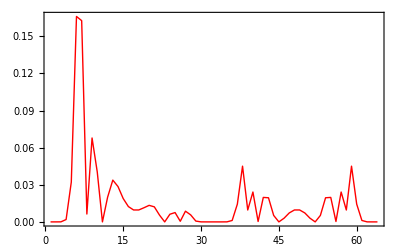

```mathematica
ListPlot[probas,PlotJoined->True,PlotStyle->{Thick,Red},Frame->True,PlotRange->All]
```

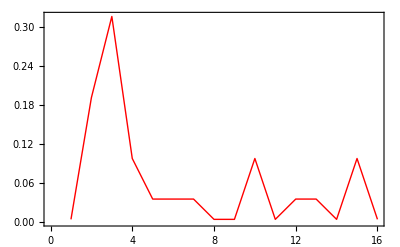

```mathematica
f1=ListPlot[{1,7,9,-5,3,-3,3,1,1,5,1,-3,3,-1,-5,-1}^2/256,PlotJoined->True,PlotStyle->{Thick,Red},Frame->True]
```

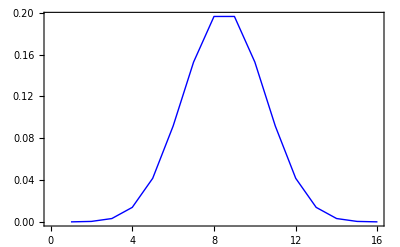

```mathematica
f2=ListPlot[Table[Binomial[15,k]/2^15,{k,0,15}],PlotJoined->True,PlotStyle->{Thick,Blue},Frame->True]
```

```mathematica
Sum[Binomial[15,k]/2^15,{k,0,15}]
```

1

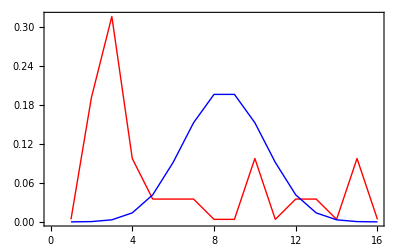

```mathematica
Show[{f1,f2}]
```